```mathematica
Clear["Global`*"]
name="/Users/tomoaki/BEM/fish/result.json"
data=Import[name];
Column[data[[;;,1]],Frame->All]
```

/Users/tomoaki/BEM/fish/result.json

bodyA_COM
bodyA_EK
bodyA_EP
bodyA_accel
bodyA_area
bodyA_force
bodyA_pitch
bodyA_roll
bodyA_torque
bodyA_velocity
bodyA_yaw
bodyB_COM
bodyB_EK
bodyB_EP
bodyB_accel
bodyB_area
bodyB_force
bodyB_pitch
bodyB_roll
bodyB_torque
bodyB_velocity
bodyB_yaw
bodyC_COM
bodyC_EK
bodyC_EP
bodyC_accel
bodyC_area
bodyC_force
bodyC_pitch
bodyC_roll
bodyC_torque
bodyC_velocity
bodyC_yaw
time
water_E
water_EK
water_EP
water_volume

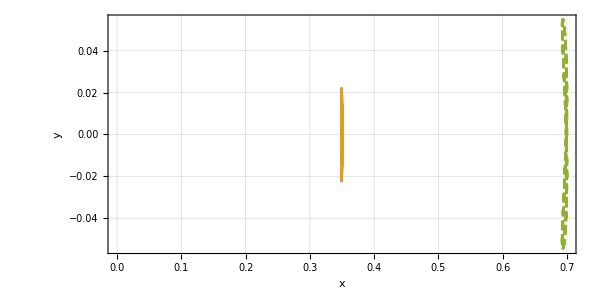

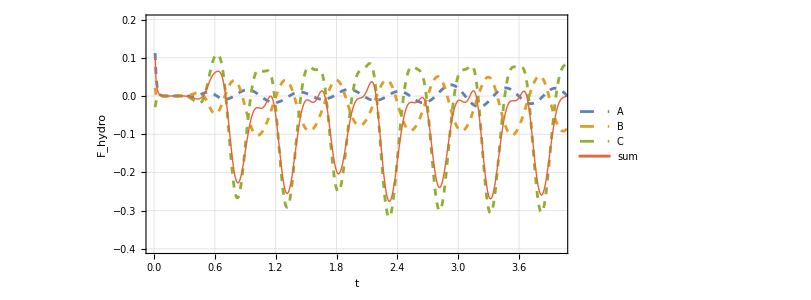

```mathematica
ListPlot[
{{#1,#2}&@@@("bodyA_COM"/.data),
{#1,#2}&@@@("bodyB_COM"/.data),
{#1,#2}&@@@("bodyC_COM"/.data)}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->Automatic
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
]

Af=#1&@@@("bodyA_force"/.data);
Bf=#1&@@@("bodyB_force"/.data);
Cf=#1&@@@("bodyC_force"/.data);

ListPlot[
{Transpose@{"time"/.data,#1&@@@("bodyA_force"/.data)},
Transpose@{"time"/.data,#1&@@@("bodyB_force"/.data)},
Transpose@{"time"/.data,#1&@@@("bodyC_force"/.data)},
Transpose@{"time"/.data,Af+Bf+Cf}}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->{{0,4},{-0.4,0.2}}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["F_hydro",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{A,B,C,sum}
]
```

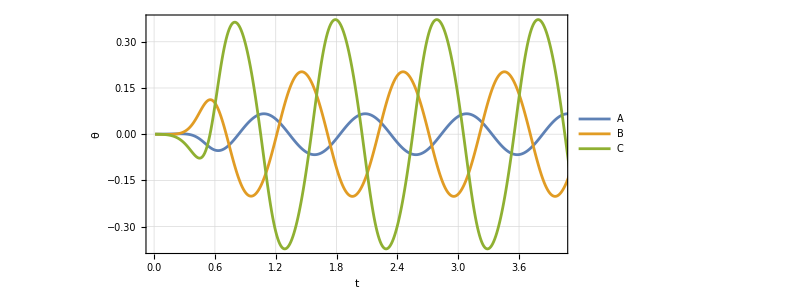

```mathematica
ListPlot[
{Transpose@{("time"/.data),("bodyA_yaw"/.data)},$Failed
Transpose@{("time"/.data),("bodyB_yaw"/.data)},
Transpose@{("time"/.data),("bodyC_yaw"/.data)}}
,Joined->True
,PlotRange->{{0,4},Automatic}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["θ",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{A,B,C,sum}
]
```